## Import data files and create interpolation objects

Form factors  span the range q = 1 to 2000 keV and E = 1 eV to 2 keV. 
q is the momentum transfer [in keV] and E is the electron kinetic energy [in keV].
Data is optimised for q = 1 to 500 keV and E = 1 eV to 1 keV. 
Interpolation outside this range is not accurate.

```mathematica
SetDirectory[NotebookDirectory[]];
LXe1sgrid=Import["Xe_1s_grid.dat"];
LXe2sgrid=Import["Xe_2s_grid.dat"];
LXe3sgrid=Import["Xe_3s_grid.dat"];
LXe4sgrid=Import["Xe_4s_grid.dat"];
LXe5sgrid=Import["Xe_5s_grid.dat"];
LXe2pgrid=Import["Xe_2p_grid.dat"];
LXe3pgrid=Import["Xe_3p_grid.dat"];
LXe4pgrid=Import["Xe_4p_grid.dat"];
LXe5pgrid=Import["Xe_5p_grid.dat"];
LXe3dgrid=Import["Xe_3d_grid.dat"];
LXe4dgrid=Import["Xe_4d_grid.dat"];
ResetDirectory[];

fXe1s=Interpolation[LXe1sgrid,InterpolationOrder->1]
fXe2s=Interpolation[LXe2sgrid,InterpolationOrder->1]
fXe3s=Interpolation[LXe3sgrid,InterpolationOrder->1]
fXe4s=Interpolation[LXe4sgrid,InterpolationOrder->1]
fXe5s=Interpolation[LXe5sgrid,InterpolationOrder->1]
fXe2p=Interpolation[LXe2pgrid,InterpolationOrder->1]
fXe3p=Interpolation[LXe3pgrid,InterpolationOrder->1]
fXe4p=Interpolation[LXe4pgrid,InterpolationOrder->1]
fXe5p=Interpolation[LXe5pgrid,InterpolationOrder->1]
fXe3d=Interpolation[LXe3dgrid,InterpolationOrder->1]
fXe4d=Interpolation[LXe4dgrid,InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«8 more identical outputs»

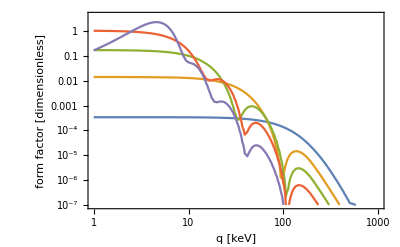

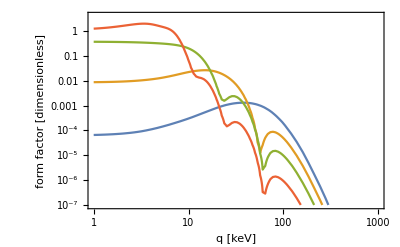

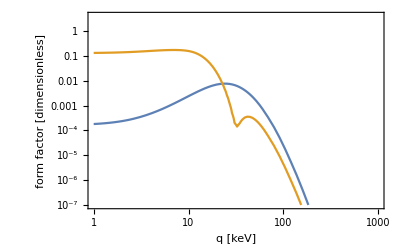

```mathematica
EtestkeV=0.025;

LogLogPlot[{fXe1s[q,EtestkeV],fXe2s[q,EtestkeV],fXe3s[q,EtestkeV],fXe4s[q,EtestkeV],fXe5s[q,EtestkeV]},{q,1,1000},PlotRange->{{1,1000},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"}]

LogLogPlot[{fXe2p[q,EtestkeV],fXe3p[q,EtestkeV],fXe4p[q,EtestkeV],fXe5p[q,EtestkeV]},{q,1,1000},PlotRange->{{1,1000},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"}]

LogLogPlot[{fXe3d[q,EtestkeV],fXe4d[q,EtestkeV]},{q,1,1000},PlotRange->{{1,1000},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"}]
```